## Exercises: Distributions

#### 1. A study on breeding birds collects information such as the length of their eggs (in mm). Assume that the length is normally distributed with μ = 42.1mm and σ^2= (20.8)^2. What is the probability of: (a) finding an egg with a length greater than 50 mm? (b) finding an egg between 30 and 40 mm in length?

(a) Our random variable X is normally distributed. Hence, the probability of finding an egg with a length greater than 50mm is equal to:

```mathematica
1.-CDF[NormalDistribution[42.1,20.8],50]
```

0.352044

(b) This can be calculated as follows:

```mathematica
N[CDF[NormalDistribution[42.1,20.8],40]-CDF[NormalDistribution[42.1,20.8],30]]
```

0.179416

That means, the probability of finding an egg between 30 and 40 mm in length is approximately 18%.

#### 2. Felix states that he is able to distinguish a freshly ground coffee blend from an ordinary supermarket coffee. One of his friends asks him to taste 10 cups of coffee and tell him which coffee he has tasted. Suppose that Felix has actually no clue about coffee and simply guesses the brand. What is the probability of at least 8 correct guesses?

Each guess is a Bernoulli experiment where the right answer is given with a probability of 50%. The number of correct guesses therefore follows a binomial distribution, i . e . X ∼ Binomial (10,0.5) . The probability of giving the right answer at least 8 times is then P(X=8)+P(X=9)+P(X=10)=1-P(X<=7). Hence:

```mathematica
1.-CDF[BinomialDistribution[10,0.5],7]
```

0.0546875

Hence, the probability that Felix guess correctly at least 8 times is approximately equal to 5.47%.

#### 3. An advertising board is illuminated by several hundred bulbs. Some of the bulbs are fused or smashed regularly. If there are more than 5 fused bulbs on a day, the owner of the board replaces them, otherwise not. Consider the following data collected over a month which captures the number of days (n_i) on which i bulbs were broken: -Graphics- (a) Suggest an appropriate distribution for X : "number of broken bulbs per day . (b) What is the average number of broken bulbs per day? What is the variance? (c) Determine the probabilities P(X = x) using the distribution you chose in (a) and using the average number of broken bulbs you calculated in (b) . Compare the probabilities with the proportions obtained from the data . (d) Calculate the probability that at least 6 bulbs are fused, which means they need to be replaced. (e) Consider the random variable Y : "time until next bulb breaks". What is the distribution of Y? (f) Calculate and interpret E (Y) .

(a) It seems appropriate to model the number of fused bulbs with a Poisson distribution. We assume, however, that the probabilities of fused bulbs on two consecutive days are independent of each other; i.e. they only depend on λ but not on the time t.
(b) The absolute frequencies for the number of days we had a certain number of fused bulbs between 0 and 5, are as follows:

```mathematica
counts={6,8,8,5,2,1}
```

{6,8,8,5,2,1}

The relative frequencies are then:

```mathematica
relfreq=N[counts/Total[counts]]
```

{0.2,0.266667,0.266667,0.166667,0.0666667,0.0333333}

Hence, we calculate the arithmetic mean for the number of broken bulbs as follows:

```mathematica
nbrokenbulbs=Range[0,5]
```

{0,1,2,3,4,5}

```mathematica
mean=Total[nbrokenbulbs*relfreq]
```

1.73333

```mathematica
N[%]
```

1.73333

Hence, on average, 1.73 bulbs are fused per day.
We can calculate the variance as follows:

```mathematica
expectedx2=Total[nbrokenbulbs^2*relfreq]
```

4.73333

```mathematica
variance=expectedx2-mean^2
```

1.72889

```mathematica
N[%]
```

1.72889

We see that the mean and the variance are very close, indicating that the choice of Poisson distribution is appropriate, because E(X)=λ and Var(X)=λ.

(c) We can compare the probabilities according to the Poisson distribution with λ=1.73 with the relative frequencies that we got as follows:

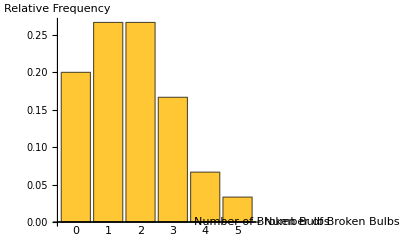

```mathematica
relfreqplot=BarChart[relfreq,ChartLabels->Placed[nbrokenbulbs,Below],AxesLabel->{"Number of Broken Bulbs","Relative Frequency"}]
```

```mathematica
poissonpmf=Table[PDF[PoissonDistribution[1.73],x],{x,0,5}]
```

{0.177284,0.306702,0.265297,0.152988,0.0661673,0.0228939}

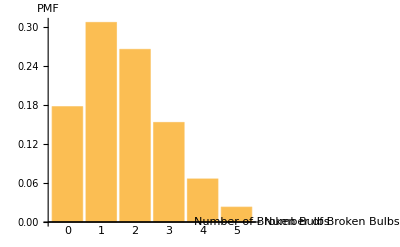

```mathematica
pmfplot=BarChart[poissondata,ChartLabels->Placed[nbrokenbulbs,Below],AxesLabel->{"Number of Broken Bulbs","PMF"}]
```

```mathematica
PairedBarChart[{relfreq},{poissonpmf},ChartLabels->nbrokenbulbs,ChartLegends->{{"rel freq", "PMF"},None,None},ChartStyle->{"Pastel",None,None}]
```

-Graphics-

(d) Using λ=1.73, we calculate P(X>5)=1-P(X≤5):

```mathematica
1.-CDF[PoissonDistribution[1.73],5]
```

0.00866697

That means that the bulbs are replaced on only 0.86% of the days.

(e) If X follows a Poisson distribution, then Y is exponentially distributed with λ=1.73 days.

(f) The expectation of an exponentially distributed variable is E(Y)=1/λ=1/1.73, that means:

```mathematica
1./1.73
```

0.578035

That means, on average, it takes more than half a day until one of the bulbs gets fused.

#### 4. A fishermen catches, on average, three fish in an hour. Let Y be a random variable denoting the number of fish caught in one hour and let X be the time interval between catching two fishes. We assume that X follows an exponential distribution. (a) What is the distribution of Y ? (b) Determine E(Y ) and E(X). (c) Calculate P(Y = 5) and P(Y < 1).

(a) The random variable Y is Poisson distributed.
(b) The fisherman catches, on average, 3 fish an hour. We can thus assume that the rate λ is 3 and thus E(Y ) = λ = 3. Similarly, E(X) = 1/λ= 1/3, which means that it takes, on average, 20 min to catch another fish.
(c) To calculate P(Y=5):

```mathematica
N[PDF[PoissonDistribution[3],5]]
```

0.100819

That means, the probability of catching 5 fish in one hour is approximately equal to 10%.
To calculate P(Y<1):

```mathematica
N[PDF[PoissonDistribution[3],0]]
```

0.0497871

That means, the probability of catching no fishes in one hour is approximately equal to 5%.